```mathematica
ints = RandomInteger[{1,100}, {100}](*task1*)
```

{7,60,22,22,61,7,60,63,33,55,10,13,97,21,12,27,32,39,71,42,13,73,23,34,45,24,63,49,18,95,4,94,21,77,88,48,42,23,68,26,29,51,44,69,31,37,57,17,67,44,52,31,64,18,92,6,18,93,56,56,91,95,27,18,58,78,35,15,36,36,85,1,13,97,31,47,71,3,54,46,8,42,10,98,62,39,41,19,52,53,22,61,8,35,11,24,82,70,76,57}

```mathematica
Cases[ints, (x_ /; Mod[x, 3] == 0)| (x_ /; Mod[x, 2] == 0)| (x_ /; Mod[x, 5] == 0)]
```

{60,22,22,60,63,33,55,10,21,12,27,32,39,42,34,45,24,63,18,95,4,94,21,88,48,42,68,26,51,44,69,57,44,52,64,18,92,6,18,93,56,56,95,27,18,58,78,35,15,36,36,85,3,54,46,8,42,10,98,62,39,52,22,8,35,24,82,70,76,57}

```mathematica
func[n_ /; IntegerQ[n]&&Positive[n]&& EvenQ[n] :=  n/2 ]
```

SetDelayed::nosym: n_/;IntegerQ[n] && Positive[n] && EvenQ[n] does not contain a symbol to attach a rule to.

func[$Failed]

```mathematica
func[ints]
```

func[{7,60,22,22,61,7,60,63,33,55,10,13,97,21,12,27,32,39,71,42,13,73,23,34,45,24,63,49,18,95,4,94,21,77,88,48,42,23,68,26,29,51,44,69,31,37,57,17,67,44,52,31,64,18,92,6,18,93,56,56,91,95,27,18,58,78,35,15,36,36,85,1,13,97,31,47,71,3,54,46,8,42,10,98,62,39,41,19,52,53,22,61,8,35,11,24,82,70,76,57}]

```mathematica
func[2]
```

func[2]

```mathematica
clear all
```

all clear

```mathematica
func
```

func

```mathematica
(*делать 2 и 3 задания*)
```

```mathematica
Solve[x^9 + 3.4 x^6 - 25 x^5 - 213 x^4 - 477 x^3 + 1012 x^2 + 111 x- 123 == 0]
```

{{x→-2.80961},{x→-1.85186-2.15082 ⅈ},{x→-1.85186+2.15082 ⅈ},{x→-0.376453},{x→0.323073},{x→1.06103-3.12709 ⅈ},{x→1.06103+3.12709 ⅈ},{x→1.30533},{x→3.13931}}

```mathematica
x /. N[%]
```

{-2.80961,-1.85186-2.15082 ⅈ,-1.85186+2.15082 ⅈ,-0.376453,0.323073,1.06103-3.12709 ⅈ,1.06103+3.12709 ⅈ,1.30533,3.13931}

```mathematica
N
```

N

```mathematica
x
```

x

```mathematica
sol = x /. N[%]
```

ReplaceAll::reps: {x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.x

```mathematica
Clear["Global`*"]
```

```mathematica
NSolve[x^9 + 3.4 x^6 - 25 x^5 - 213 x^4 - 477 x^3 + 1012 x^2 + 111 x- 123 == 0, x, Reals]
```

{{x→-2.80961},{x→-0.376453},{x→0.323073},{x→1.30533},{x→3.13931}}

```mathematica
sol = x /. N[%]
```

{-2.80961,-0.376453,0.323073,1.30533,3.13931}

```mathematica
sol
```

{-2.80961,-0.376453,0.323073,1.30533,3.13931}

```mathematica
Cases[sol, n_ /; n < 0 ]
```

{-2.80961,-0.376453}

```mathematica
Clear["Global`*"]
```

```mathematica
findRootNest[fun_,init_]:=NestWhile[#-fun[#]/fun'[#]&,N[init],Abs[fun[#] - fun[#+1]]<10^6&]
```

```mathematica
findRootNest[#^2-50&,500][x]
```

$Aborted

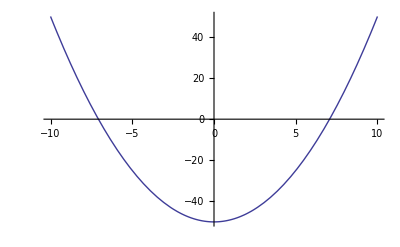

```mathematica
Plot[x^2-50,{x,-10,10}]
```

```mathematica
findRootNest[fun_,init_]:=NestWhile[#-fun[#]/fun'[#]&,N[init],Abs[fun[#] - fun[#+1]]<10^-6&]
```

```mathematica
findRootNest[#^2-50&,500][x]
```

$Aborted

```mathematica
findRootNest[#^2-50&,500]
```

$Aborted

```mathematica
findRootNest[#^2-50&,500][x]
```

$Aborted

```mathematica
Clear["Global`*"]
```

```mathematica
Plot[x^2-50,{x,-10,10}]
```

-Graphics-

```mathematica
findRootNest[fun_,init_]:=NestWhile[#-fun[#]/fun'[#]&,N[init],Abs[fun[#] - fun[#+1]]>10^-6&]
```

```mathematica
findRootNest[#^2-50&,500]
```

$Aborted

```mathematica
findRootNest[#^2-50&,50]
```

50.

```mathematica
findRootNestList[fun_,init_]:=NestWhileList[#-fun[#]/fun'[#]&,N[init],Abs[fun[#] - fun[#+1]]<10^-3&]
```

```mathematica
findRootNestList[#^2 - 50&,500]
```

```mathematica
{500.}
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*задание 3 сделать*)
```